```mathematica
v=9;
l=100;
vv=ToString[v];
ll=ToString[l];
FBD0[l]={{0,0}};
FBD1[l]={{0,0}};
FBD2[l]={{0,0}};
FBD3[l]={{0,0}};
FBDratio[l]={{0,0}};

For[i=0,i<150,i++,
d=0.001+i*0.001;
dd=ToString[d];
FBD[l][i]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/FrequentBrakeDis-v"<>vv<>"-d"<>dd<>"-l"<>ll<>"k.txt",{Number,Number}];
FBD0[l]=Append[FBD0[l],{d,FBD[l][i][[1]][[2]]}];
FBD1[l]=Append[FBD1[l],{d,FBD[l][i][[2]][[2]]}];
FBD2[l]=Append[FBD2[l],{d,FBD[l][i][[3]][[2]]}];
FBD3[l]=Append[FBD3[l],{d,FBD[l][i][[4]][[2]]}];

FBDratio[l]=Append[FBDratio[l],{d,FBD[l][i][[3]][[2]]/FBD[l][i][[2]][[2]]}]

]
FBD0[l]=Delete[FBD0[l],1];
FBD1[l]=Delete[FBD1[l],1];
FBD2[l]=Delete[FBD2[l],1];
FBD3[l]=Delete[FBD3[l],1];
FBDratio[l]=Delete[FBDratio[l],1];
```

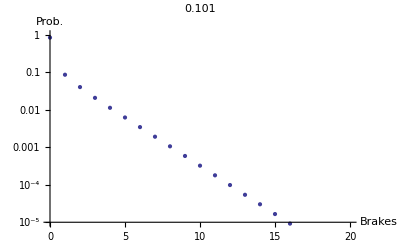

```mathematica
l=30;
x=100;
ListLogPlot[FBD[l][x],PlotRange->{{0,20},{0.00001,1}},PlotLabel->0.001+x*0.001,AxesLabel->{"Brakes","Prob."},PlotLabel->l  x]
```

```mathematica
ListAnimate[Table[ListLogPlot[FBD[l][x],PlotRange->{{0,15},{0.00001,0.3}},PlotLabel->0.001+x*0.001,AxesLabel->{"Brakes","Prob."}],{x,149}]]
```

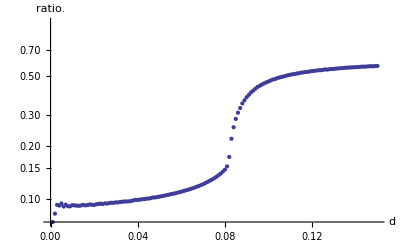

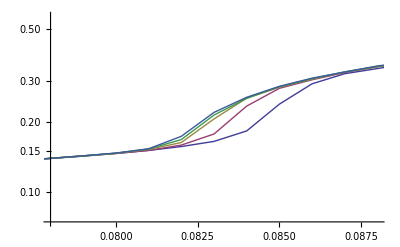

```mathematica
ListLogPlot[FBDratio[50],PlotLegend->{"(Prob. 2 Brake)/(Prob. 1 Brake)"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","ratio."}]
ListLogPlot[{FBDratio[5],FBDratio[10],FBDratio[20],FBDratio[30],FBDratio[50]},PlotRange->{{0.078,0.088},Full},Joined->True]
```

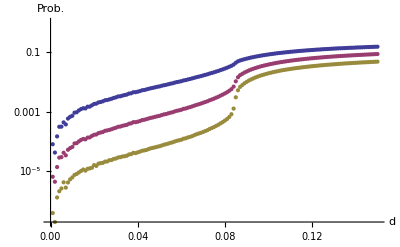

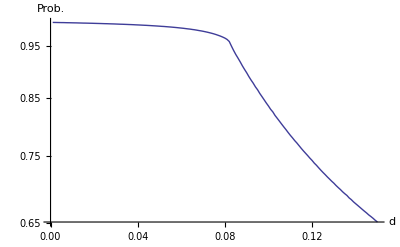

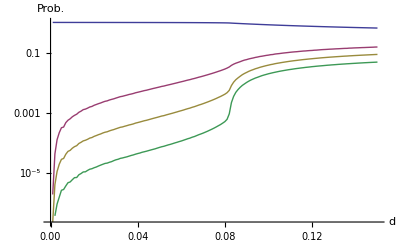

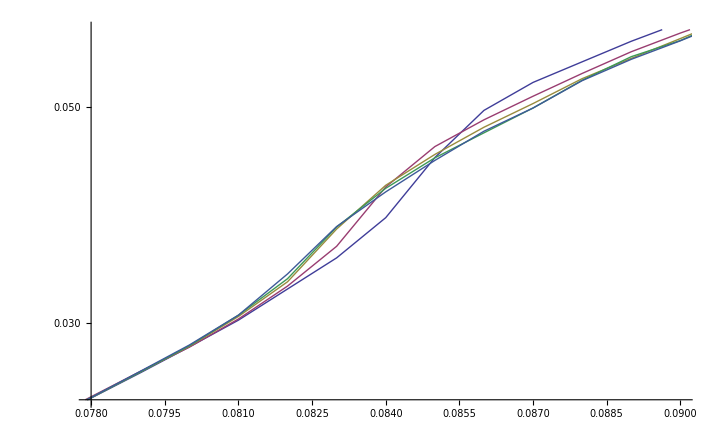

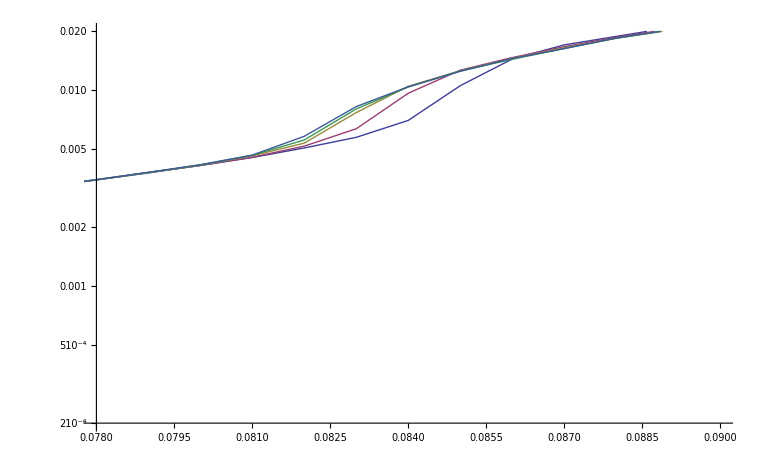

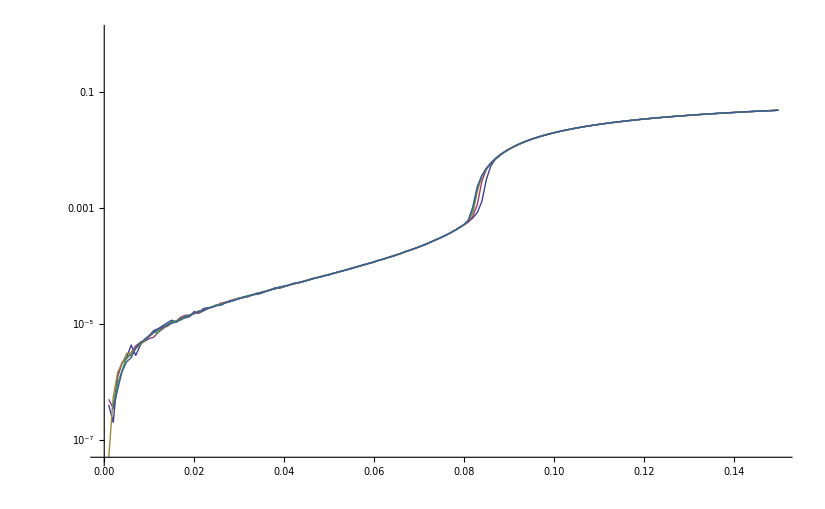

```mathematica
ListLogPlot[{FBD1[5],FBD2[5],FBD3[5]},PlotLegend->{"1 Brake","2 Brakes","3 Brakes"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Prob."}]
ListLogPlot[{FBD0[30]},Joined->True,PlotLegend->{"No Brake"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Prob."}]
ListLogPlot[{FBD0[30],FBD1[30],FBD2[30],FBD3[30]},Joined->True,PlotLegend->{"No Brake","1 Brake","2 Brakes","3 Brakes"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Prob."}]
ListLogPlot[{FBD1[5],FBD1[10],FBD1[20],FBD1[30],FBD1[50]},Joined->True,PlotRange->{{0.078,0.09},{0.025,0.06}}]
ListLogPlot[{FBD2[5],FBD2[10],FBD2[20],FBD2[30],FBD2[50]},Joined->True,PlotRange->{{0.078,0.09},{0.0002,0.02}}]
ListLogPlot[{FBD3[5],FBD3[10],FBD3[20],FBD3[30],FBD3[50]},Joined->True]
```

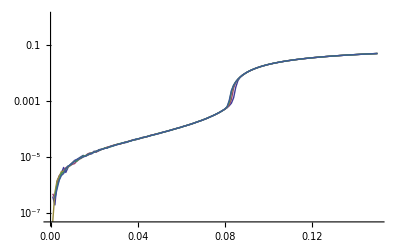

```mathematica
ListLogPlot[{FBD3[5],FBD3[10],FBD3[20],FBD3[30],FBD3[50]},Joined->True]
```

```mathematica
FBDI1=Interpolation[FBD1[l]];
```

```mathematica
FBDI1[0.082]
```

0.0332886

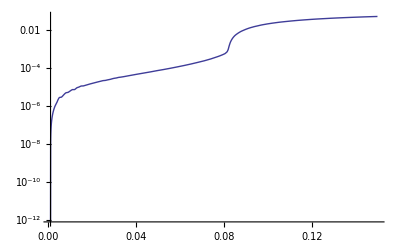

```mathematica
LogPlot[FBDI3[x],{x,0.001,0.15}]
```

```mathematica
h=0.002;
derr[l]=Table[{i*0.001,(FBDI3[i*0.001+h]-2*FBDI3[i*0.001]+FBDI3[i*0.001-h])/(h*h)},{i,5,120}];
```

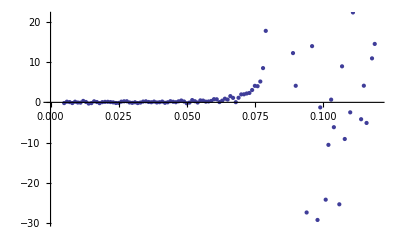

```mathematica
ListPlot[derr[l]]
```

```mathematica
d=0.18;
ND[FBDI1[x],{x,2},d]
```

-53618.

```mathematica
FBDI3=Interpolation[FBD3[l]];
```

```mathematica
FBD1der[l]={{0,0}};
FBD1der2[l]={{0,0}};

For[i=0,i<150,i++,
d=0.001+i*0.001;
dd=ToString[d];


FBD1der[l]=Append[FBD1der[l],{d,ND[FBDI3[x],{x,1},d]}];
FBD1der2[l]=Append[FBD1der2[l],{d,ND[FBDI3[x],{x,2},d]}];


]

FBD1der[l]=Delete[FBD1der[l],1];
FBD1der2[l]=Delete[FBD1der2[l],1];
```

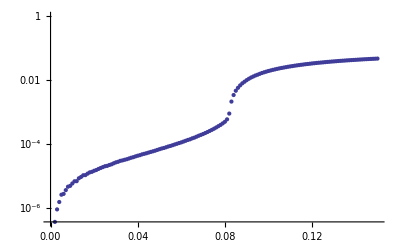

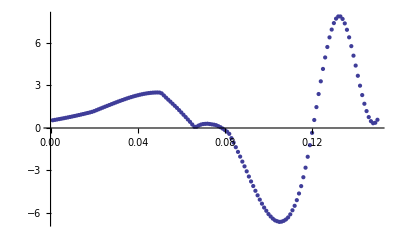

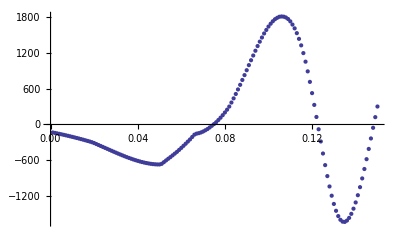

```mathematica
ListLogPlot[FBD3[l]]
ListPlot[FBD1der[l]]
ListPlot[FBD1der2[l]]
```